## Set your working directory here.

```mathematica
SetDirectory["<<ENTER YOUR WORKING DIRECTORY>>"];
```

## Calculation takes 21.8 hours.

```mathematica
N[78470/3600]
```

21.7972

## Lowest temperature configuration

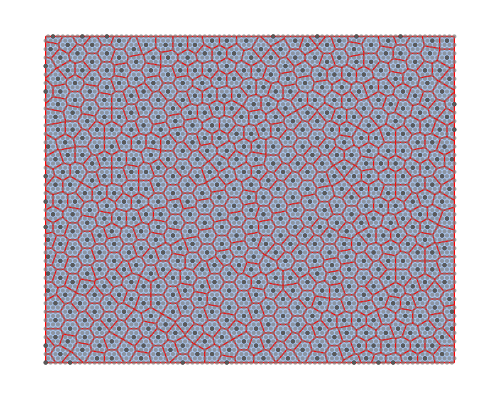
-Graphics--Graphics-

```mathematica
rgb[x_,y_,z_]:=RGBColor[x/255,y/255,z/255];
c1=rgb[102,194,165];
c2=rgb[252,141,98];
c3=rgb[141,160,203];
c4=rgb[231,138,195];
c5=rgb[166,216,84];
c6=rgb[255,217,47];
pall=Function[x,Blend[Transpose[{{0,4/40,7/40,9/40,12/40,13/40,16/40,40/40},{Black,c1,c2,c3,c4,c5,c6,Black}}],x]];
inPolyQ[poly_,pt_]:=Graphics`PolygonUtils`PointWindingNumber[poly,pt]=!=0;
findnerve[ctr_,primitives_]:=Cases[primitives,Polygon[p__]/;(ContainsAny[p,ctr[[1]]]&&p≠ctr[[1]])]
tiling[datain_]:=Module[{data0=datain,vor,mp,polys,poly,np,lps,d,npolys,list,case,analy},
vor=VoronoiMesh[data0,N[{{-.2,side1+.2},{-.2,Sqrt[3]side2/2+.2}}]];
mp=MeshPrimitives[vor,2];
polys={};
Do[
poly=Table[If[inPolyQ[mp[[i]],data0[[k]]]==True,mp[[i]],Nothing],{i,Length[mp]}][[1]];
npolys=findnerve[poly,mp];
list=Table[DeleteDuplicates[npolys[[i,1]]],{i,Length[npolys]}];
case=DeleteDuplicates[poly[[1]]];
analy=Table[If[MemberQ[case,list[[j,i]]]==True,1,Nothing],{j,Length[list]},{i,Length[list[[j]]]}];
analy=Table[If[Length[analy[[i]]]==2,1,0],{i,Length[analy]}];
npolys=Table[If[analy[[i]]==1,npolys[[i]],Nothing],{i,Length[analy]}];
np=Flatten[Table[If[inPolyQ[npolys[[j]],data0[[i]]]==True,data0[[i]],Nothing],{j,Length[npolys]},{i,Length[data0]}],1];
AppendTo[polys,Table[Check[ConvexHullMesh[N[{Nearest[poly[[1]],np[[i]],2][[1]],data0[[k]],np[[i]],Nearest[poly[[1]],np[[i]],2][[2]]}],MeshCellStyle->{2->Opacity[1.,pall[EuclideanDistance[np[[i]],data0[[k]]]^2/40]],1->Opacity[0.]}],Nothing],{i,Length[np]}]];
,{k,Length[data0]}];
polys=Flatten[polys,1];
(*Show[polys,Graphics[{PointSize[.009],Point[data0]}],ImageSize->1000,Background->Black]*)
Image[ImageCrop[Show[polys,Graphics[{PointSize[.009],Point[data0]}],ImageSize->1000,Background->Black],800],ImageSize->500]
];
side1=84;
side2=78;
data=Import["konf_latt_tri_int_barr_1_J_-0_800737_C_1_0_radij_24_mrad_1_ls_4_5_side1_84_side2_78_N_622_ni_22500_intv_1_intt_50_tempz_0_01_tempk_0_001_tempi_-0_00003.dat"];
coor=N[Table[{If[i+j/2>side1,i+j/2-side1,i+j/2],Sqrt[3]j/2},{i,side1},{j,side2}]];
coorf=Flatten[coor,1];
data=Flatten[Table[If[data[[i,j]]==1,coor[[i,j]],Nothing],{i,side1},{j,side2}],1];
Row[{VoronoiMesh[data,N[{{Min[coorf[[All,1]]],Max[coorf[[All,1]]]},{Min[coorf[[All,2]]],Max[coorf[[All,2]]]}}],MeshCellHighlight->{{1,All}->Red},Epilog->{{Black,Point[data]},{Opacity[.7],Gray,Point[coorf]}},ImageSize->500],tiling[data]}]
```

## Configurations over the whole temperature range

```mathematica
side1=84;
side2=78;
data=ArrayReshape[Flatten[Import["all_konf_latt_tri_int_barr_1_J_-0_800737_C_1_0_radij_24_mrad_1_ls_4_5_side1_84_side2_78_N_622_ni_22500_intv_1_intt_50_tempz_0_01_tempk_0_001_tempi_-0_00003.dat"]],{300,side1,side2}];
coor=N[Table[{If[i+j/2>side1,i+j/2-side1,i+j/2],Sqrt[3]j/2},{i,side1},{j,side2}]];
coorf=Flatten[coor,1];
data=Table[Flatten[Table[If[data[[i,j,k]]==1,coor[[j,k]],Nothing],{j,side1},{k,side2}],1],{i,300}];
vor=Table[VoronoiMesh[data[[i]],N[{{Min[coorf[[All,1]]],Max[coorf[[All,1]]]},{Min[coorf[[All,2]]],Max[coorf[[All,2]]]}}],MeshCellHighlight->{{1,All}->Red},Epilog->{{Black,Point[data[[i]]]},{Opacity[.7],Gray,Point[coorf]}},ImageSize->500],{i,300}];
Manipulate[vor[[i]],{i,1,300,1}]
```

Part::partd: Part specification vor⟦300⟧ is longer than depth of object.

## Energy versus temperature plot

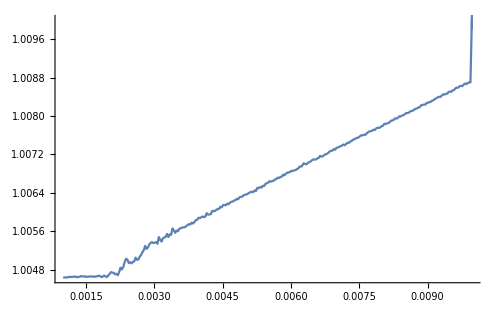

```mathematica
Needs["ErrorBarPlots`"];
side1=84;
side2=78;
data=Import["en_latt_tri_int_barr_1_J_-0_800737_C_1_0_radij_24_mrad_1_ls_4_5_side1_84_side2_78_N_622_ni_22500_intv_1_intt_50_tempz_0_01_tempk_0_001_tempi_-0_00003.dat"];
ErrorListPlot[Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,Length[data]}],ImageSize->500,Joined->True,PlotRange->All]
```

## Heat capacity vs temperature plot

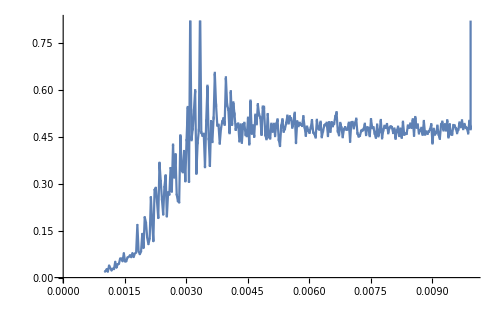

```mathematica
Needs["ErrorBarPlots`"];
side1=84;
side2=78;
data=Import["cv_latt_tri_int_barr_1_J_-0_800737_C_1_0_radij_24_mrad_1_ls_4_5_side1_84_side2_78_N_622_ni_22500_intv_1_intt_50_tempz_0_01_tempk_0_001_tempi_-0_00003.dat"];
ErrorListPlot[Table[{{data[[i,1]],data[[i,2]]},ErrorBar[data[[i,3]]]},{i,Length[data]}],ImageSize->500,Joined->True]
```